-Graphics3D-

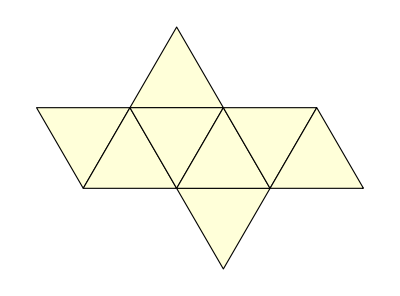

{{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,6},{3,5},{3,6},{4,5},{4,6},{5,6}}

-Graphics3D-

```mathematica
(* use octahedron function*)
Graphics3D[Octahedron[], Boxed->False]
PolyhedronData["Octahedron", "Net"]
vertices=PolyhedronData["Octahedron","VertexCoordinates"];
edges = PolyhedronData["Octahedron", "EdgeIndices"]
faces = PolyhedronData["Octahedron", "FaceIndices"];Graphics3D[{PolyhedronData["Octahedron","Faces"],Table[Text[Style[i,Bold,16],vertices[[i]]],{i,Length[vertices]}]},Boxed->False]
```